```mathematica
eq = a0 Coth[ArcSinh[a0/a]] == b;
Solve[eq,a0]
```

Solve::ivar: 2 √21 is not a valid variable.

Solve[True,2 √21]

```mathematica
b= 10;
d =2 b; 
a = 4;
a0=Sqrt[-a*a+b*b];
(*a0 = 10;*)
num = -ArcSinh[a0/a];
(* From (A,B,ϕ) to (ξ,η) *)
ξ = 2 ArcTan[ArcTanh[A]];
η = 1/ArcTanh[B]+num;
```

```mathematica
(* From (ξ,η) to (x,ρ,ϕ) *)
x1 = TrigExpand[a0 Sinh[η]/(Cosh[η]-Cos[ξ])];
ρ = TrigExpand[a0 Sin[ξ]/(Cosh[η]-Cos[ξ])];
```

```mathematica
(* From (x,ρ,ϕ) to (x,y,z) *)
x = x1;
y = (ρ)Cos[ϕ];
z = (ρ)Sin[ϕ];
```

```mathematica
eq = Expand[TrigReduce[FullSimplify[(x-a0 Coth[-ArcSinh[a0/a]])^2 +y^2 + z^2 == (a)^2]]];
```

```mathematica
sol =Solve[eq&& A>0 && A<1&& B<1&&B>-1,B, Reals]
```

{}

```mathematica
sol1 = B/.sol[[1,1]];
(*sol2 = B/.sol[[2,1]];*)
```

```mathematica
pl1 = Plot[sol1, {A,0, 1}, PlotStyle-> Red, PlotRange->All];
(*pl2 = Plot[sol2,{A,0,Tanh[Pi]}, PlotStyle->{Red,Dashed}, PlotRange->All];*)
```

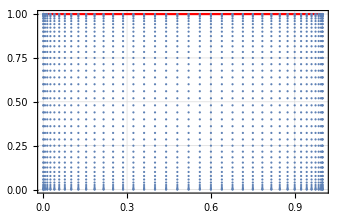

```mathematica
na = 40;
nb=40;
Ai = Table[ Sin[Pi i/(2(na-1))]^2,{i,0,na,1}];
Bi = Table[ Sin[Pi i/(2(nb-1))]^2,{i,0,nb,1}];

sol11 = Table[sol1/.A->Ai[[i]],{i,1,na+1,1}];
(*sol21 = Table[sol2/.A->Ai[[i]],{i,1,na+1,1}];*)

points1 = Tuples[{Ai,Bi}];

pl3 = ListPlot[points1];

Show[pl1,pl3,Frame-> True, GridLines->Automatic]
```